```mathematica
ClearAll["Global`*"]
```

## Random Testing:

```mathematica
A=Import["C:\\Users\\Himanshu\\Desktop\\Julia\\Base code for positron transport\\HydrogenXS.csv"]
```

{{Energy,Total,Ps,Direct,Ann,Excitation ,Process,Threshold},{0.01,13.2033,0,0,0.0000996,0,Ps,6.8},{0.02,11.8169,0,0,0.0000704,0,Dir,13.6},1567,{4990,0.0999,0,0.0248,1.41×10^-7,0.0000212,,},{5000,0.0997,0,0.0248,1.41×10^-7,0,,}}
 |  |  |  |

```mathematica
Tot=A[[2;;1567,2]];
Elas = A[[2;;1567,2]]-A[[2;;1567,3]]-A[[2;;1567,4]]-A[[2;;1567,5]]-A[[2;;1567,6]];
```

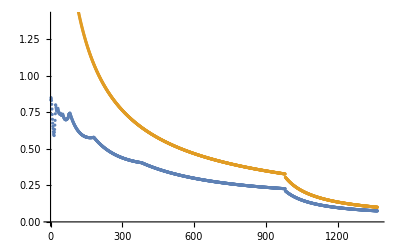

```mathematica
bs=ListPlot[{Elas[[200;;All]],Tot[[200;;All]]}]
```

```mathematica
Fit[Elas[[200;;All]],{1,x},x]
```

0.111892-0.0000728525 x

0.707289-0.000826235 x+2.77406×10^-7 x^2

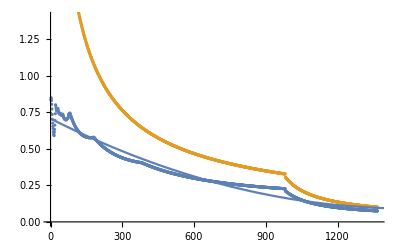

```mathematica
as=Fit[Elas[[200;;All]],{1,x,x*x},x]
Plot[as,{x,0,1500}];
Show[bs,%]
```

-5.38236+6.1651 ⅇ^(-x/1000)+0.00463219 x-1.33061×10^-6 x^2

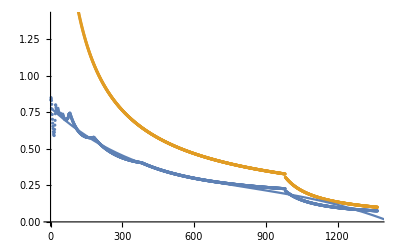

```mathematica
as=Fit[Elas[[200;;All]],{1,x,x*x,Exp[-x/1000]},x]
Plot[as,{x,0,1500}];
Show[bs,%]
```

{{v→                                 8
InterpolatingFunction[{{1., 1. 10 }}, <>]}}

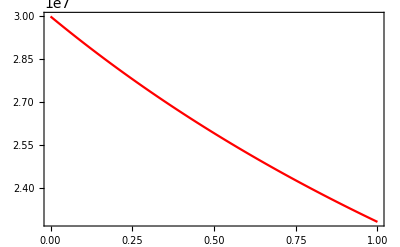

```mathematica
α = 3.5*^7;
β = 1/2000;
σ[x_] :=.6*^-20;
Subscript[v, 0] = 3*10^7;
Subscript[v, m] = 800;
range = 10^8;

Needs["DifferentialEquations`NDSolveUtilities`"];

sol=NDSolve[{v'[t]== -α * σ[v[t]]*v[t]^2*(β - Subscript[v, m]^2/v[t]^2),v[0]==Subscript[v, 0]},v,{t,1,range}]
Plot[Evaluate[v[t]/.sol], {t, 1, range}, 
PlotStyle -> {Red}, Axes -> False, Frame -> True]
```

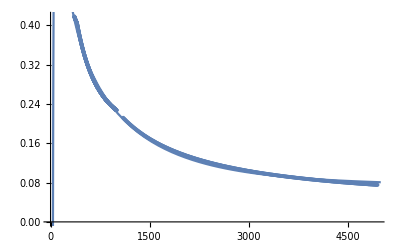

0.0644953+0.241011 ⅇ^(-x/1000)+73.5579/(0.1+x)-3132.55/(0.3+x)^2

```mathematica
A=Import["C:\\Users\\Himanshu\\Desktop\\Julia\\Base code for positron transport\\HydrogenXS.csv"];
Tot=A[[2;;1567,2]];
Energy = A[[2;;1567,1]];
Elas = A[[2;;1567,2]]-A[[2;;1567,3]]-A[[2;;1567,4]]-A[[2;;1567,5]]-A[[2;;1567,6]];


data=Thread[{Energy,Elas}][[270;;All]];
fit=Fit[data,{1,1/(x+.1),1/(x+.3)^2,Exp[-x/1000]},x];
Plot[fit,{x,0,5000}];
Show[{ListPlot[data[[270;;All]]],%}]
fit
```

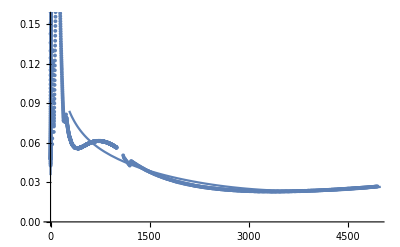

0.04717-0.000015591 x+2.16885×10^-9 x^2-17.0461/(10+x)^2+15.8749/(100+x)

```mathematica
A=Import["C:\\Users\\Himanshu\\Desktop\\Julia\\Base code for positron transport\\HeliumXS.csv"];
Tot=A[[2;;1567,2]];
Energy = A[[2;;1567,1]];
Elas = A[[2;;1567,2]]-A[[2;;1567,3]]-A[[2;;1567,4]]-A[[2;;1567,5]]-A[[2;;1567,6]];

Cutoff= 20;
data=Thread[{Energy,Elas}][[Cutoff;;All]];
fit=Fit[data,{1,1/(x+100),x/1000,x*x/10000,1/(x+10)^2},x];
Plot[fit,{x,0,5000}];
Show[{ListPlot[Thread[{Energy,Elas}][[1;;All]]],%}]
fit
```

## Hydrogen:

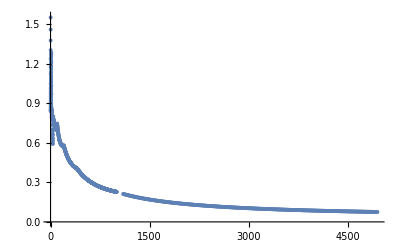

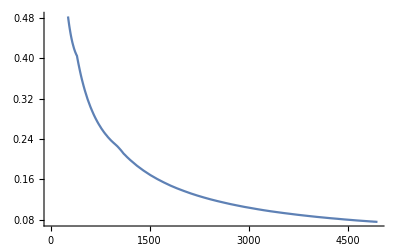

{{v→                                 8
InterpolatingFunction[{{1., 1. 10 }}, <>]}}

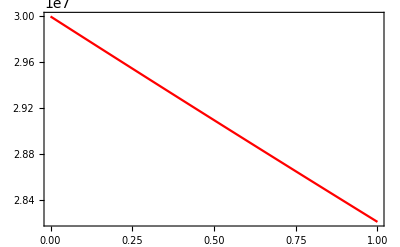

```mathematica
A=Import["C:\\Users\\Himanshu\\Desktop\\Julia\\Base code for positron transport\\HydrogenXS.csv"];
Tot=A[[2;;1567,2]];
Energy = A[[2;;1567,1]];
Elas = A[[2;;1567,2]]-A[[2;;1567,3]]-A[[2;;1567,4]]-A[[2;;1567,5]]-A[[2;;1567,6]];
data=Thread[{Energy,Elas}];
f=Interpolation[data];
ListPlot[data]
Plot[f[x],{x,0.01,4950}]
α = 3.5*^7;
β = 1/2000;
σ[x_] :=f[2.8437499999999995*^-12 x^2]*10^-20;
Subscript[v, 0] = 3*10^7;
Subscript[v, m] = 800;
range = 10^8;

Needs["DifferentialEquations`NDSolveUtilities`"];

sol=NDSolve[{v'[t]== -α * σ[v[t]]*v[t]^2*(β - Subscript[v, m]^2/v[t]^2),v[0]==Subscript[v, 0]},v,{t,1,range}]
Plot[Evaluate[v[t]/.sol], {t, 1, range}, 
PlotStyle -> {Red}, Axes -> False, Frame -> True]
```

## Helium:

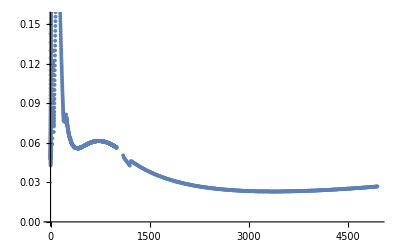

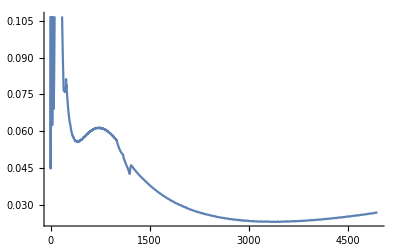

{{v→                                 8
InterpolatingFunction[{{1., 1. 10 }}, <>]}}

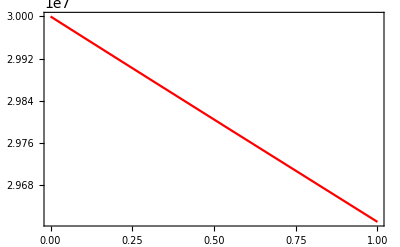

```mathematica
A=Import["C:\\Users\\Himanshu\\Desktop\\Julia\\Base code for positron transport\\HeliumXS.csv"];
Tot=A[[2;;1567,2]];
Energy = A[[2;;1567,1]];
Elas = A[[2;;1567,2]]-A[[2;;1567,3]]-A[[2;;1567,4]]-A[[2;;1567,5]]-A[[2;;1567,6]];
data=Thread[{Energy,Elas}];
f=Interpolation[data,InterpolationOrder->2];
ListPlot[data]
Plot[f[x],{x,0.01,4950}]


α = 3.5*^7;
β = 1/2000;
σ[x_] :=f[2.8437499999999995*^-12 x^2]*10^-20;
Subscript[v, 0] = 3*10^7;
Subscript[v, m] = 800;
range = 10^8;

Needs["DifferentialEquations`NDSolveUtilities`"];

sol=NDSolve[{v'[t]== -α * σ[v[t]]*v[t]^2*(β - Subscript[v, m]^2/v[t]^2),v[0]==Subscript[v, 0]},v,{t,1,range}]
Plot[Evaluate[v[t]/.sol], {t, 1, range}, 
PlotStyle -> {Red}, Axes -> False, Frame -> True]
```